```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 170 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[q]
q = { θ1[t] , θ2[t] }
```

{θ1[t],θ2[t]}

```mathematica
Clear[r]
r = { l Sin[θ1[t]] + L Sin[θ2[t]] , - l Cos[θ1[t]]-L Cos[θ2[t]] }
```

{l Sin[θ1[t]]+L Sin[θ2[t]],-l Cos[θ1[t]]-L Cos[θ2[t]]}

```mathematica
D[r, t]
```

{l Cos[θ1[t]] θ1'[t]+L Cos[θ2[t]] θ2'[t],l Sin[θ1[t]] θ1'[t]+L Sin[θ2[t]] θ2'[t]}

```mathematica
D[r, t] . D[r, t]
```

(l Cos[θ1[t]] θ1'[t]+L Cos[θ2[t]] θ2'[t])^2+(l Sin[θ1[t]] θ1'[t]+L Sin[θ2[t]] θ2'[t])^2

```mathematica
D[r, t] . D[r, t]  // Expand
```

l^2 Cos[θ1[t]]^2 θ1'[t]^2+l^2 Sin[θ1[t]]^2 θ1'[t]^2+2 l L Cos[θ1[t]] Cos[θ2[t]] θ1'[t] θ2'[t]+2 l L Sin[θ1[t]] Sin[θ2[t]] θ1'[t] θ2'[t]+L^2 Cos[θ2[t]]^2 θ2'[t]^2+L^2 Sin[θ2[t]]^2 θ2'[t]^2

```mathematica
D[r, t] . D[r, t]  // Expand  // Simplify
```

l^2 θ1'[t]^2+2 l L Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+L^2 θ2'[t]^2

```mathematica
Clear[T]
T = ( D[r, t] . D[r, t]  // Expand  // Simplify ) + 1/2(1/3 M L^2 θ2'[t]^2)
```

l^2 θ1'[t]^2+2 l L Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+L^2 θ2'[t]^2+1/6 L^2 M θ2'[t]^2

```mathematica
Clear[V] 
V = - M g ( l Cos[θ1[t] ]+ L Cos[θ1[t]] )
```

-g M (l Cos[θ1[t]]+L Cos[θ1[t]])

```mathematica
(* This needs to be derived *) 
Clear[U]
U = - F ( l Sin[θ1[t]] + 2 L Sin[θ2[t]] )
```

-F (l Sin[θ1[t]]+2 L Sin[θ2[t]])

```mathematica
Clear[ℒ]
ℒ = T - V -U
```

g M (l Cos[θ1[t]]+L Cos[θ1[t]])+F (l Sin[θ1[t]]+2 L Sin[θ2[t]])+l^2 θ1'[t]^2+2 l L Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+L^2 θ2'[t]^2+1/6 L^2 M θ2'[t]^2

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q , t ] ;
eqs //Expand //  TableForm
```

F l Cos[θ1[t]]-g l M Sin[θ1[t]]-g L M Sin[θ1[t]]-2 l L Sin[θ1[t]-θ2[t]] θ2'[t]^2-2 l^2 θ1''[t]-2 l L Cos[θ1[t]-θ2[t]] θ2''[t]==0
2 F L Cos[θ2[t]]+2 l L Sin[θ1[t]-θ2[t]] θ1'[t]^2-2 l L Cos[θ1[t]-θ2[t]] θ1''[t]-2 L^2 θ2''[t]-1/3 L^2 M θ2''[t]==0

```mathematica
Clear[ics]
ics = { 
θ1[0] == 0.2,
θ1'[0] == 0.2,
θ2[0] == 0.2,
θ2'[0] == 0.2
} ;
ics // TableForm
```

θ1[0]==0.2
θ1'[0]==0.2
θ2[0]==0.2
θ2'[0]==0.2

```mathematica
Clear[parameters]
parameters = {
M->   10,
g-> 9.8 ,
L-> 2,
l-> 4 , 
F-> 1 
};
parameters // TableForm
```

M→10
g→9.8
L→2
l→4
F→1

```mathematica
eqs //. parameters
```

{4 Cos[θ1[t]]-588. Sin[θ1[t]]-16 Sin[θ1[t]-θ2[t]] θ2'[t]^2-32 θ1''[t]-16 Cos[θ1[t]-θ2[t]] θ2''[t]==0,-2/3 (-6 Cos[θ2[t]]-24 Sin[θ1[t]-θ2[t]] θ1'[t]^2+24 Cos[θ1[t]-θ2[t]] θ1''[t]+32 θ2''[t])==0}

```mathematica
Clear[solution]
solution[t_] = First[NDSolve[
Union[ eqs //. parameters , ics ] , q , { t, 0, 100 } ] ]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t]  ] , { t, 0, 10 } , PlotLabels-> q ]
```

-Graphics-

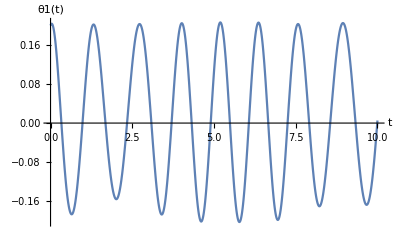

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t]  ] , { t, 0, 10 } , AxesLabel-> { t , q[[1]]  } ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

θ1[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax }  , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.1 , 20 } ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

θ2[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

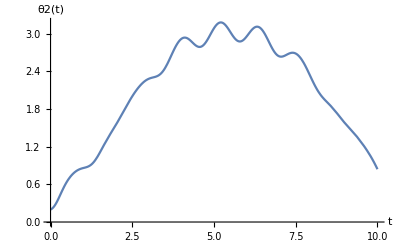

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t]  ] , { t, 0, 10 } , AxesLabel-> { t , q[[2]] } ]
```

```mathematica
Animate[
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] }]  , { tmax , 0.1 , 20 } ]
```